```mathematica
ass=Assumptions->{kx,ky,kz,k,θ,ϕ,θp,ϕp,kp,cq,vf,B,μ,fac,βintra} ∈ Reals && k>0 && kf>0 &&  0<=θ<=π && 0<=θp<=π && βintra>0 &&  vf>0;
rep={kx->kf Sin[θ] Cos[ϕ],ky->kf Sin[θ] Sin[ϕ],kz->kf Cos[θ]};
rep1={kx->Subscript[k, x],ky->Subscript[k, y],kz->Subscript[k, z],θ->γ,θp->γ^p,Bz->Subscript[B, z],kf->Subscript[k, F],vf->Subscript[v, 0]};
```

## phys quantities

```mathematica
rep={kx->k Sin[θ] Cos[ϕ],ky->k Sin[θ] Sin[ϕ],kz->k Cos[θ]};Bz=B;
kfass=Assumptions->{kx,ky,kz,k,θ,ϕ,θp,ϕp,kp,vinter,vinter} ∈ Reals && k>0 && kp>0 && 0<=θ<=π && 0<=θp<=π && vintra>0 && vinter>0;
en0=vf √(kx^2+ky^2+kz^2);
Print["band vel."];
v0=FullSimplify[Grad[en0,{kx,ky,kz}]/.rep,ass]
Print["v0.k"];
v0dotk=FullSimplify[v0.{kx,ky,kz}/.rep,Assumptions->k ∈ Reals && k>0]
Print["BC vector"];(* -Graphics-*)
Ω(* {(kx kz)/((kx^2+ky^2+kz^2)^2),(ky kz)/((kx^2+ky^2+kz^2)^2),kz^2/((kx^2+ky^2+kz^2)^2)}*)=(chi  kz)/((kx^2+ky^2+kz^2)^2){ kx ,ky ,kz};FullSimplify[Ω/.rep,ass]
ommvec=(-chi e vf kz)/(2(kx^2+ky^2+kz^2)^(3/2)){kx,ky,kz};
Print["OMM energy"];
enom=-ommvec.{0,0,Bz};
FullSimplify[enom/.rep,ass]
Print["OMM correc. to band vel."];
vm=FullSimplify[Grad[enom,{kx,ky,kz}],ass]
FullSimplify[vm/.rep,ass]
Print["vm.k"];
vmdotk=FullSimplify[vm.{kx,ky,kz}/.rep,Assumptions->k ∈ Reals && k>0]
Print["v.Ω"];
FullSimplify[(v0+vm).Ω/.rep,Assumptions->k ∈ Reals && k>0]
```

band vel.

{vf Cos[ϕ] Sin[θ],vf Sin[θ] Sin[ϕ],vf Cos[θ]}

v0.k

k vf

BC vector

{(chi Cos[θ] Cos[ϕ] Sin[θ])/k^2,(chi Cos[θ] Sin[θ] Sin[ϕ])/k^2,(chi Cos[θ]^2)/k^2}

OMM energy

(B chi e vf Cos[θ]^2)/(2 k)

OMM correc. to band vel.

{-(3 B chi e kx kz^2 vf)/(2 (kx^2+ky^2+kz^2)^(5/2)),-(3 B chi e ky kz^2 vf)/(2 (kx^2+ky^2+kz^2)^(5/2)),(B chi e kz (2 (kx^2+ky^2)-kz^2) vf)/(2 (kx^2+ky^2+kz^2)^(5/2))}

{-(3 B chi e vf Cos[θ]^2 Cos[ϕ] Sin[θ])/(2 k^2),-(3 B chi e vf Cos[θ]^2 Sin[θ] Sin[ϕ])/(2 k^2),-(B chi e vf (Cos[θ]+3 Cos[3 θ]))/(8 k^2)}

vm.k

-(B chi e vf Cos[θ]^2)/(2 k)

v.Ω

-(chi vf Cos[θ] (B chi e-4 k^2+B chi e Cos[2 θ]))/(4 k^4)

## Fermi surface

```mathematica
FullSimplify[Flatten[SolveValues[vf kf+(Bz e vf  Cos[θ]^2)/(2 kf)==μ,kf],1],ass]
```

{(μ-√(μ^2-2 B e vf^2 Cos[θ]^2))/(2 vf),(μ+√(μ^2-2 B e vf^2 Cos[θ]^2))/(2 vf)}

```mathematica
(* +ve Bz*)(Solve[vf kf+vf(absBz e)/(2 kf) ctsq==μ,ctsq]//Flatten)/.absBz->Bz
(* -ve Bz*)(Solve[vf kf-vf(absBz e)/(2 kf) ctsq==μ,ctsq]//Flatten)(*/.absBz->-Bz*)
```

{ctsq→-(2 kf (kf vf-μ))/(B e vf)}

{ctsq→(2 kf (kf vf-μ))/(absBz e vf)}

```mathematica
exp=vf kf+(Bz e vf Cos[θ]^2)/(2  vf)/.rep1;
TeXForm[exp]
```

\frac{1}{2} e B_z \cos ^2(\gamma )+v_0 k_F

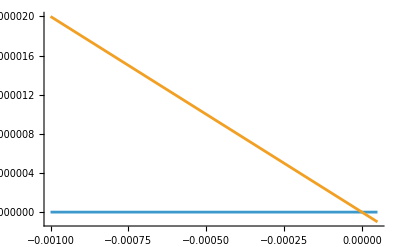

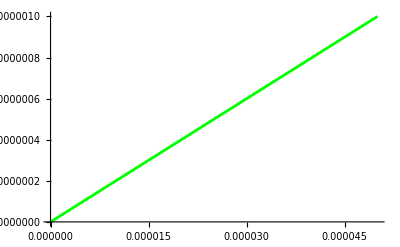

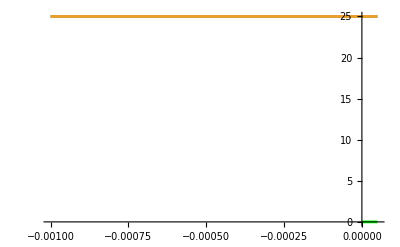

```mathematica
mu=0.01;Bzval=mu^2/2;vfval=0.0004;
p1=Plot[{ mu/vfval,(mu+√(mu^2-2 B  vfval^2))/(2 vfval) },{B,-0.001,mu^2/2},PlotRange->{0,All}]
p2=Plot[{ (mu-√(mu^2-2 B  vfval^2))/(2 vfval)},{B,-0.001,mu^2/2},PlotStyle->Green,PlotRange->{0,All}]
Show[{p1,p2},PlotRange->{0,All}]
(*Plot[{mu/vfval,(mu+√(mu^2-2 Bzval  Cos[θ]^2))/(2 vfval)},{θ,π/2-0.01,π/2+0.01},PlotRange->All]*)
```

```mathematica
(* OMM *)
bval=-0.1;k=1;fn=k+4(bval Cos[θ]^2)/k;fs=SphericalPlot3D[fn,{θ,0,π},{ϕ,0,2 π},Mesh->None,PlotStyle->Directive[Cyan,Opacity[0.5],Specularity[50]],Lighting->"Neutral",(*PlotPoints->300,*)BaseStyle->{FontFamily->"TexMaths Symbols",24,Black,Bold},LabelStyle->Black,Axes->True,Ticks->False,AxesLabel->{"k_z","k_x","k_y"},AxesOrigin->{0,0,0},Boxed->False,ImageSize->300]
SetDirectory[NotebookDirectory[]];
Clear[k];
```

```mathematica
Reduce[vf kf+(vf eBz)/(2 kf)>0 && eBz<0 && kf>0 && vf>0, eBz]
```

vf>0&&kf>0&&-2 kf^2<eBz<0

```mathematica
Reduce[(μ+√(μ^2-2 eBz vf vf))/(2 vf)>0 && eBz>0 && μ>0 && vf>0, eBz]
Reduce[(μ+√(μ^2-2 eBz vf vf))/(2 vf)>0 && eBz<0 && μ>0 && vf>0, eBz]
```

vf>0&&μ>0&&0<eBz≤μ^2/(2 vf^2)

μ>0&&vf>0&&eBz<0

```mathematica
Reduce[(μ-√(μ^2-2 eBz vf vf))/(2 vf)>0 && eBz>0 && μ>0 && vf>0, eBz]
Reduce[(μ-√(μ^2-2 eBz vf vf))/(2 vf)>0 && eBz<0 && μ>0 && vf>0, eBz]
```

vf>0&&μ>0&&0<eBz≤μ^2/(2 vf^2)

False

## Matrix forms

```mathematica
Clear[G];(* -Graphics-*)
G=(3+4ct ctp+c2t c2tp)/8;
```

```mathematica
Clear[eq,Λbyτ,lhs1,lhs2,lhs3,lhs4,rhs1,rhs2,rhs3,rhs4,λ,a,b,h11,h21,h10,c11,eqn1,eqn2,eqn3,eqn4,eqn5,eqn6];
Λbyτ=(-h1+λ1+a1 ct(* Cos[θ] *)+b1 c2t(* Cos[2θ]*));

(* -Graphics- ; -Graphics-; -Graphics-*)
lhs1=λ1+a1 ct+b1 c2t;     rhs1=β intθpf1 G(-h1+λ1+a1 ctp+b1 c2tp);

eq=lhs1-rhs1;
eqn1=SeriesCoefficient[eq,{ct,0,0},{c2t,0,0}]//FullSimplify
eqn2=SeriesCoefficient[eq,{ct,0,1},{c2t,0,0}]//FullSimplify
eqn3=SeriesCoefficient[eq,{ct,0,0},{c2t,0,1}]//FullSimplify
eq==eqn1+eqn2 ct+eqn3 c2t//FullSimplify

(* Print["charge consvn:"];*)
intθf1 Λbyτ
```

λ1-3/8 intθpf1 β (b1 c2tp+a1 ctp-h1+λ1)

a1-1/2 ctp intθpf1 β (b1 c2tp+a1 ctp-h1+λ1)

b1-1/8 c2tp intθpf1 β (b1 c2tp+a1 ctp-h1+λ1)

True

intθf1 (b1 c2t+a1 ct-h1+λ1)

```mathematica
Clear[arr,array,cmat];arr=CoefficientArrays[{eqn1==0,eqn2==0,eqn3==0},{λ1,a1,b1}];
array=Normal[arr]//Simplify;
cmat=array[[2]]//Simplify;
rep={intθpf1->af1,c2tp->c2t,ctp->ct};
cmat=Expand[cmat/.rep];
array[[1]]=Expand[array[[1]]/.rep];
MatrixForm[cmat]//FullSimplify
MatrixForm[array[[1]]]//FullSimplify
```

(1-(3 af1 β)/8 | -3/8 af1 ct β | -3/8 af1 c2t β
-1/2 af1 ct β | 1-1/2 af1 ct^2 β | -1/2 af1 c2t ct β
-1/8 af1 c2t β | -1/8 af1 c2t ct β | 1-1/8 af1 c2t^2 β)

((3 af1 h1 β)/8
1/2 af1 ct h1 β
1/8 af1 c2t h1 β)

```mathematica
(* ({{1-3 zero β, -3 ct β, -3 c2t β}, {-4 ct β, 1-4 af1 ctsq β, -4 ctc2t β}, {-c2t β, -af1 ctc2t β, 1-af1 c2tsq β}}) and  β({{3 hzero}, {4 hct}, {hc2t}})*)
```

## sigma

```mathematica
(*-Graphics-*)
```

```mathematica
Clear[sig,sol1,sol2,sol3];
sig[B_,μ_,v0_,β_]:=Block[{e=1,BCvec,v0vec,vf=v0,vmvec,matr,rhs1,rhs2,θ,τ,kf,f,vdotk,cs,λ1,a1,b1,cost,θp,ϕ,Dphase,h,hzero,hct,hc2t,zero,ct,c2t,ctsq,c2tsq,ctc2t,colvec,mat,sol,sol1,sol2,sol3,Λ1,s1,int1},
kf[θ_]=  (μ+√(μ^2-2vf vf  B e Cos[θ]^2))/(2 vf);
BCvec[θ_]=Cos[θ]/kf[θ]^2{ Cos[ϕ] Sin[θ], Sin[θ] Sin[ϕ],Cos[θ]};
Dphase[θ_]=1 +e (BCvec[θ])[[3]] B;
v0vec[θ_]=vf{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ], Cos[θ]};
(*{-(3 B chi e vf Cos[θ]^2 Cos[ϕ] Sin[θ])/(2 k^2),-(3 B chi e vf Cos[θ]^2 Sin[θ] Sin[ϕ])/(2 k^2),-(B chi e vf (Cos[θ]+3 Cos[3 θ]))/(8 k^2)}*)
vmvec[θ_]=- vf  e B{(3  Cos[θ]^2 Cos[ϕ] Sin[θ])/(2 kf[θ]^2),(3 Cos[θ]^2 Sin[θ] Sin[ϕ])/(2 kf[θ]^2),(Cos[θ]+3 Cos[3 θ])/(8 kf[θ]^2)};
vdotk[θ_]=kf[θ] vf-(B e vf  Cos[θ]^2)/(2 kf[θ]);(* -(B chi e vf Cos[θ]^2)/(2 k) *)
h[θ_]=1/Dphase[θ]((v0vec[θ]+vmvec[θ])[[3]]-e B (vf Cos[θ] (B e-4 kf[θ]^2 +B e Cos[2 θ]))/(4 kf[θ]^4));(* -(chi vf Cos[θ] (B chi e-4 k^2+B chi e Cos[2 θ]))/(4 k^4) *)
(*******-Graphics-*)
τ[θ_]=(1/8 3β Quiet[NIntegrate [(Sin[θp] (kf[θp])^3)/Abs[vdotk[θp]] Dphase[θp],{θp,0,π}]]+
1/8 4β Cos[θ] Quiet[NIntegrate [(Sin[θp] (kf[θp])^3)/Abs[vdotk[θp]] Dphase[θp]Cos[θp],{θp,0,π}]]+1/8 β Cos[2θ] Quiet[NIntegrate [(Sin[θp] (kf[θp])^3)/Abs[vdotk[θp]] Dphase[θp]Cos[2θp],{θp,0,π}]])^-1;

f[θ_]=(Sin[θ] (kf[θ])^3)/Abs[vdotk[θ]] Dphase[θ] τ[θ];
zero=Quiet[NIntegrate [f[θp],{θp,0,π}]];
ct=Quiet[NIntegrate [f[θp] Cos[θp],{θp,0,π}]];
ctsq=Quiet[NIntegrate [f[θp] Cos[θp]^2,{θp,0,π}]];
c2t=Quiet[NIntegrate [f[θp] Cos[2θp],{θp,0,π}]];
c2tsq=Quiet[NIntegrate [f[θp] Cos[2θp]^2,{θp,0,π}]];
ctc2t=Quiet[NIntegrate [f[θp]Cos[θp] Cos[2θp],{θp,0,π}]];

hzero=Quiet[NIntegrate [f[θp] h[θp],{θp,0,π}]];
hct=Quiet[NIntegrate [f[θp]h[θp]Cos[θp],{θp,0,π}]];
hc2t=Quiet[NIntegrate [f[θp]h[θp]Cos[2θp],{θp,0,π}]];
colvec= β/8 ({{3 hzero}, {4 hct}, {hc2t}});(* ({{(3 af1 h1 β)/8}, {1/2 af1 ct h1 β}, {1/8 af1 c2t h1 β}}) *)
mat=({{1-3 zero β/8, -3 ct β/8, -3 c2t β/8}, {- ct β/2, 1-  ctsq β/2, - ctc2t β/2}, {-c2t β/8, - ctc2t β/8, 1- c2tsq β/8}});(*({{1-(3 af1 β)/8, -3/8 af1 ct β, -3/8 af1 c2t β}, {-1/2 af1 ct β, 1-1/2 af1 ct^2 β, -1/2 af1 c2t ct β}, {-1/8 af1 c2t β, -1/8 af1 c2t ct β, 1-1/8 af1 c2t^2 β}})*)

matr=mat.{λ1,a1,b1};
cs=λ1 zero-hzero+a1 ct+b1 c2t;
(*sol1=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,cs==0},{λ1,a1,b1}],1];
sol2=Flatten[Solve[{matr[[2]]+colvec[[2]]==0,matr[[3]]+colvec[[3]]==0,cs==0},{λ1,a1,b1}],1];*)
sol3=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,matr[[3]]+colvec[[3]]==0,cs==0},{λ1,a1,b1}],1];

sol=sol3;

Λ1[θ_]=(-h[θ]+λ1+a1 Cos[θ]+b1 Cos[2θ])/.sol;

(* -Graphics- *)
int1[θ_]=-f[θ]h[θ]Λ1[θ];

s1=Quiet[NIntegrate[int1[θ],{θ,0,π}]];
{B,s1(*, cs/.sol,MatrixRank[mat,Tolerance->10^(-4)],Det[mat],MatrixForm[{λ1,a1,b1}/.sol]*)}
];

mu=0.01;Bval=-mu^2/2;vfval=0.0004;ampli=1;
(* sig[B_,μ_,v0_,βintra_] *)
sig[Bval,mu,vfval, ampli]
```

{-0.00005,2.6838×10^-7}

### sigma at B=0

```mathematica
Clear[sig0];
sig0[μ_,v0_,β_]:=Block[{e=1,B=0,BCvec,v0vec,vf=v0,vmvec,matr,rhs1,rhs2,θ,τ,kf,f,vdotk,cs,λ1,a1,b1,cost,θp,ϕ,Dphase,h,hzero,hct,hc2t,zero,ct,c2t,ctsq,c2tsq,ctc2t,colvec,mat,sol,sol1,sol2,sol3,Λ1,s1,int1},
kf[θ_]= μ/vf ;
Dphase[θ_]=1 ;
v0vec[θ_]=vf{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ], Cos[θ]};
vmvec[θ_]={ 0,0,0};
vdotk[θ_]=kf[θ] vf;
h[θ_]=(v0vec[θ])[[3]];
(***************)
τ[θ_]=(3β Quiet[NIntegrate [(Sin[θp] (kf[θp])^3)/(8Abs[vdotk[θp]])Dphase[θp],{θp,0,π}]]+
4β Cos[θ] Quiet[NIntegrate [(Sin[θp] (kf[θp])^3)/(8Abs[vdotk[θp]])Dphase[θp]Cos[θp],{θp,0,π}]]+β Cos[2θ] Quiet[NIntegrate [(Sin[θp] (kf[θp])^3)/(8Abs[vdotk[θp]])Dphase[θp]Cos[2θp],{θp,0,π}]])^-1;

f[θ_]=(Sin[θ] (kf[θ])^3)/Abs[vdotk[θ]] Dphase[θ] τ[θ];
zero=Quiet[NIntegrate [f[θp],{θp,0,π}]];
ct=Quiet[NIntegrate [f[θp] Cos[θp],{θp,0,π}]];
ctsq=Quiet[NIntegrate [f[θp] Cos[θp]^2,{θp,0,π}]];
c2t=Quiet[NIntegrate [f[θp] Cos[2θp],{θp,0,π}]];
c2tsq=Quiet[NIntegrate [f[θp] Cos[2θp]^2,{θp,0,π}]];
ctc2t=Quiet[NIntegrate [f[θp]Cos[θp] Cos[2θp],{θp,0,π}]];

hzero=Quiet[NIntegrate [f[θp] h[θp],{θp,0,π}]];
hct=Quiet[NIntegrate [f[θp]h[θp]Cos[θp],{θp,0,π}]];
hc2t=Quiet[NIntegrate [f[θp]h[θp]Cos[2θp],{θp,0,π}]];
colvec= β/8 ({{3 hzero}, {4 hct}, {hc2t}});
mat=({{1-3 zero β/8, -3 ct β/8, -3 c2t β/8}, {-4 ct β/8, 1-4  ctsq β/8, -4 ctc2t β/8}, {-c2t β/8, - ctc2t β/8, 1- c2tsq β/8}});

matr=mat.{λ1,a1,b1};
cs=λ1 zero-hzero+a1 ct+b1 c2t;

sol1=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,cs==0},{λ1,a1,b1}],1];
sol2=Flatten[Solve[{matr[[2]]+colvec[[2]]==0,matr[[3]]+colvec[[3]]==0,cs==0},{λ1,a1,b1}],1];
sol3=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,matr[[3]]+colvec[[3]]==0,cs==0},{λ1,a1,b1}],1];

sol=sol3;

Λ1[θ_]=(λ1-h[θ]+a1 Cos[θ]+b1 Cos[2θ])/.sol;
int1[θ_]=-f[θ]h[θ]Λ1[θ];

s1=Quiet[NIntegrate[int1[θ],{θ,0,π}]];
{0,s1(*cs/.sol,MatrixForm[{λ1,a1,b1}/.sol],MatrixRank[mat],Det[mat]*)}
];
mu=0.01;vfval=0.0004;ampli=1;
(* sig0[μ_,v0_,βintra_] *)
sig0[mu,vfval, ampli]
```

{0,2.6838×10^-7}

## Results

### set 1

```mathematica
mu=0.01;v0val=0.0004;ampli=1;lim=mu^2/(2.1*v0val*v0val)
s0=sig0[mu,v0val,ampli]
dat=Table[Quiet[sig[B,mu,v0val,ampli]],{B,-50,50,100/20}]
```

297.619

{0,2.6838×10^-7}

{{-50,2.43537×10^-7},{-45,2.45996×10^-7},{-40,2.48461×10^-7},{-35,2.50932×10^-7},{-30,2.53409×10^-7},{-25,2.55893×10^-7},{-20,2.58381×10^-7},{-15,2.60874×10^-7},{-10,2.63372×10^-7},{-5,2.65874×10^-7},{0,2.6838×10^-7},{5,2.7089×10^-7},{10,2.73402×10^-7},{15,2.75917×10^-7},{20,2.78434×10^-7},{25,2.80953×10^-7},{30,2.83473×10^-7},{35,2.85994×10^-7},{40,2.88515×10^-7},{45,2.91036×10^-7},{50,2.93556×10^-7}}

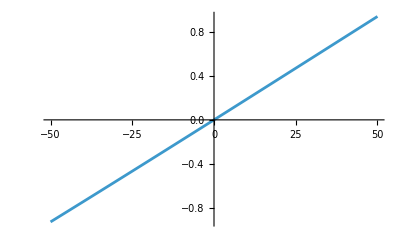

```mathematica
scale={0,2.683803498399426*^-7};list={{-50,2.4353740896448745*^-7},{-45,2.459957149332449*^-7},{-40,2.484607163939792*^-7},{-35,2.509320818361714*^-7},{-30,2.5340947239950667*^-7},{-25,2.5589254152983536*^-7},{-20,2.5838093461448324*^-7},{-15,2.608742885953232*^-7},{-10,2.633722315578775*^-7},{-5,2.6587438229455496*^-7},{0,2.6838034983994314*^-7},{5,2.708897329758708*^-7},{10,2.734021197037356*^-7},{15,2.759170866813221*^-7},{20,2.78434198621066*^-7},{25,2.8095300764639534*^-7},{30,2.8347305260240723*^-7},{35,2.859938583167571*^-7},{40,2.885149347415905*^-7},{45,2.91035776423205*^-7},{50,2.9355586093891416*^-7}};
len=Length[list];
dat1=Table[{list[[i,1]],(list[[i,2]]/scale[[2]]-1)×10^1},{i,1,len}];
p1=ListLinePlot[dat1,PlotRange->{{-50,50},All}]
```

### set 2

```mathematica
mu=0.03;v0val=0.0004;ampli=1;lim=mu^2/(2.1*v0val*v0val)
s0=sig0[mu,v0val,ampli]
dat=Table[Quiet[sig[B,mu,v0val,ampli]],{B,-50,50,100/20}]
```

2678.57

{0,2.6838×10^-7}

{{-50,2.65596×10^-7},{-45,2.65874×10^-7},{-40,2.66153×10^-7},{-35,2.66431×10^-7},{-30,2.66709×10^-7},{-25,2.66988×10^-7},{-20,2.67266×10^-7},{-15,2.67545×10^-7},{-10,2.67823×10^-7},{-5,2.68102×10^-7},{0,2.6838×10^-7},{5,2.68659×10^-7},{10,2.68938×10^-7},{15,2.69216×10^-7},{20,2.69495×10^-7},{25,2.69774×10^-7},{30,2.70053×10^-7},{35,2.70332×10^-7},{40,2.70611×10^-7},{45,2.7089×10^-7},{50,2.71169×10^-7}}

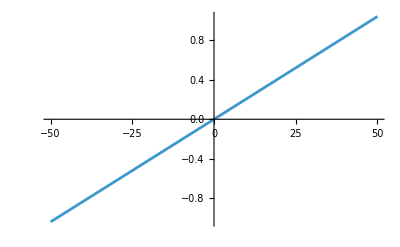

```mathematica
scale={0,2.683803498399426*^-7};
list={{-50,2.655961698242466*^-7},{-45,2.6587438229455475*^-7},{-40,2.66152641896372*^-7},{-35,2.664309480857541*^-7},{-30,2.667093003171867*^-7},{-25,2.669876980435765*^-7},{-20,2.672661407162415*^-7},{-15,2.6754462778497744*^-7},{-10,2.678231586977138*^-7},{-5,2.6810173290107705*^-7},{0,2.683803498399431*^-7},{5,2.6865900895755415*^-7},{10,2.689377096955108*^-7},{15,2.69216451493762*^-7},{20,2.694952337905949*^-7},{25,2.697740560225388*^-7},{30,2.7005291762467203*^-7},{35,2.70331818030189*^-7},{40,2.7061075667064077*^-7},{45,2.7088973297587057*^-7},{50,2.7116874637400387*^-7}};
len=Length[list];
dat2=Table[{list[[i,1]],(list[[i,2]]/scale[[2]]-1)×10^2},{i,1,len}];
p2=ListLinePlot[dat2,PlotRange->{{-50,50},{Automatic,Automatic}}]
```

### set 3

```mathematica
mu=0.05;v0val=0.0004;ampli=1;lim=mu^2/(2.1*v0val*v0val)
s0=sig0[mu,v0val,ampli]
dat=Table[Quiet[sig[B,mu,v0val,ampli]],{B,-50,50,100/20}]
```

7440.48

{0,2.6838×10^-7}

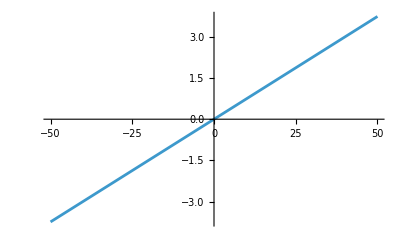

```mathematica
scale={0,2.6838034983994267*^-7};
list={{-50,2.673775302471601*^-7},{-45,2.674777868690961*^-7},{-40,2.675780491904315*^-7},{-35,2.676783171853838*^-7},{-30,2.6777859082814417*^-7},{-25,2.6787887009287676*^-7},{-20,2.6797915495371775*^-7},{-15,2.680794453847768*^-7},{-10,2.6817974136013583*^-7},{-5,2.6828004285384877*^-7},{0,2.683803498399432*^-7},{5,2.684806622924183*^-7},{10,2.685809801852463*^-7},{15,2.6868130349237126*^-7},{20,2.687816321877096*^-7},{25,2.6888196624515033*^-7},{30,2.68982305638555*^-7},{35,2.6908265034175593*^-7},{40,2.6918300032855874*^-7},{45,2.6928335557274074*^-7},{50,2.6938371604805094*^-7}};
len=Length[list];
dat3=Table[{list[[i,1]],(list[[i,2]]/scale[[2]]-1)×10^3},{i,1,len}];
p3=ListLinePlot[dat3,PlotRange->{{-50,50},{Automatic,Automatic}}]
```

## Final Plots

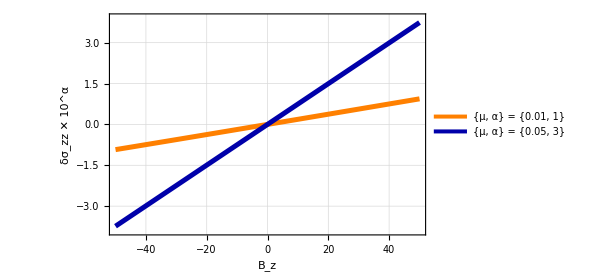

```mathematica
thk=0.007;
style={Directive[Orange,Thickness[0.008]](***),(**)Directive[Darker[Blue],Thickness[0.008]],(**)Directive[Darker[Cyan],Thickness[0.008]]};
leg=LineLegend[style,{"{μ, α} = {0.01, 1}","{μ, α} = {0.05, 3}"},LabelStyle->{FontFamily->"Times",20,Bold,Darker[Gray]},LegendLayout->"Row"];

pl=ListLinePlot[{dat1,dat3},PlotRange->{{-50,50},{-3.9,3.9}},PlotStyle->style,GridLines->Automatic,LabelStyle->{Black,Bold,22,FontFamily->"Times"},Frame->True,Axes->False,FrameLabel->{"B_z","δσ_zz ✕ 10^α"},FrameTicksStyle->Directive[Bold,Gray,14],ImageSize->450,PlotLegends->Placed[leg,Below]]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["bcd-sigz.pdf",Rasterize[pl,Background->None],ImageResolution->100];
```